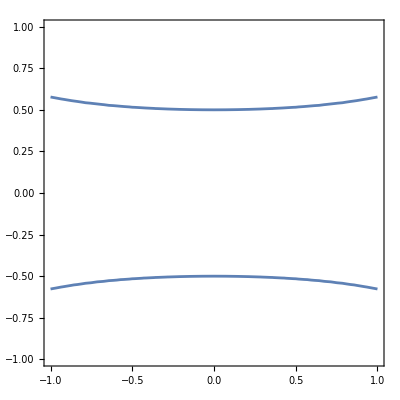

0

ArcTan[x/(√(4-x^2))]

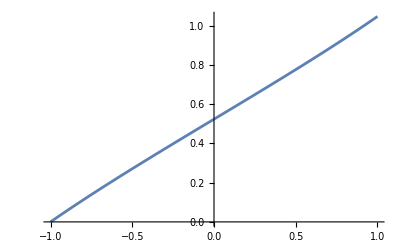

{{h→1/(3 k)}}

{{h→2/(3 (1+2 k))}}

```mathematica
(*Задача
-h^2 d/dx (4-x^2) d/dx u = u
u(-1)=0, u(1)=0*)
ContourPlot[(4-x^2)*p^2==1,{x,-1,1},{p,-1,1}]
H0[x_,p_]:=(4-x^2)*p^2-1;
H1[x_,p_]:=I*2*x*p;
FullSimplify[1/2*D[H0[x,p],x,p]-I*H1[x,p]]
Integrate[1/Sqrt[4-x^2],x]
S[x_]:=ArcTan[x/(√(4-x^2))]-ArcTan[-1/Sqrt[3]];
J[x_]:=2*Sqrt[4-x^2];
Plot[S[x],{x,-1,1}]
Manipulate[Plot[Im[Exp[I*S[x]/h]/Sqrt[J[x]]+Exp[-I*Pi]*Exp[-I*S[x]/h]/Sqrt[J[x]]],{x,-1,1}],{h,0.001,0.1}]
Solve[1/(Pi*h)*S[1]==k,h]
hDir[k_]:=1/(3 k);
Solve[1/(Pi*h)*S[1]==1/2+k,h]
hDirNeum[k_]:=2/(3 (1+2 k));
Manipulate[Plot[Im[Exp[I*S[x]/hDir[k]]/Sqrt[J[x]]+Exp[-I*Pi]*Exp[-I*S[x]/hDir[k]]/Sqrt[J[x]]],{x,-1,1}],{k,1,20,1}]
Manipulate[Show[Plot[Im[Exp[I*S[x]/hDirNeum[k]]/Sqrt[J[x]]+Exp[-I*Pi]*Exp[-I*S[x]/hDirNeum[k]]/Sqrt[J[x]]],{x,-1,1}],Plot[(Im[Exp[I*S[1]/hDirNeum[k]]/Sqrt[J[1]]+Exp[-I*Pi]*Exp[-I*S[1]/hDirNeum[k]]/Sqrt[J[1]]]),{x,0,1},PlotStyle->{Red,Dashed}]],{k,1,20}]
Manipulate[Show[Plot[Re[Exp[I*S[x]/hDir[k]]/Sqrt[J[x]]+Exp[-I*S[x]/hDir[k]]/Sqrt[J[x]]],{x,-1,1}],Plot[(Re[Exp[I*S[1]/hDir[k]]/Sqrt[J[1]]+Exp[-I*S[1]/hDir[k]]/Sqrt[J[1]]]),{x,0,1},PlotStyle->{Red,Dashed}],Plot[(Re[Exp[I*S[-1]/hDir[k]]/Sqrt[J[-1]]+Exp[-I*S[-1]/hDir[k]]/Sqrt[J[-1]]]),{x,-1,0},PlotStyle->{Green,Dashed}]],{k,1,20}]
Manipulate[Show[Plot[Re[Exp[I*S[x]/hDirNeum[k]]/Sqrt[J[x]]+Exp[-I*S[x]/hDirNeum[k]]/Sqrt[J[x]]],{x,-1,1}],Plot[(Re[Exp[I*S[-1]/hDirNeum[k]]/Sqrt[J[-1]]+Exp[-I*S[-1]/hDirNeum[k]]/Sqrt[J[-1]]]),{x,-1,0},PlotStyle->{Green,Dashed}]],{k,1,20}]
```

```mathematica
N[(1/2 x √(4-x^2)+2 ArcTan[x/(√(4-x^2))])/.x->1]
```

1.91322